```mathematica
(* Computer Graphics with Applications of Dr. Makhanov *)
```

```mathematica
(* Lecture 2. 2D and 3D Graphics. Polar Plots. 2D Graphics primitives *)
```

```mathematica
SetOptions[{Plot,Plot3D,ParametricPlot,ParametricPlot3D,PolarPlot,Graphics},ImageSize->Small];
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False, Background -> White];
```

```mathematica
(* We introduce 2 ways to define numerical functions  *)
```

```mathematica
(* 1) f1[arguments or list of arguments_]:={list of outputs} *)
```

```mathematica
(* Example 01. Explicit function f:R1->R1*)
```

```mathematica
f0[t_]:=Sin[t^2]+Log[t]
```

```mathematica
(* Call, graph: *)
```

```mathematica
f0[10] (*careful with value inside the log function -> log(0) = - infinity . therefore avoid*)
```

```mathematica
(* The plot is saved in the variable Pexplicit0 *)
```

```mathematica
Pexplicit0=Plot[f0[t],{t,0,5}] (*plot 2d graph using the the function, with value t range 0.1 to 5*)
```

```mathematica
(*doesn't cause an error when ploting result of infinity*)
```

```mathematica
(*plot the graph, assign plot data to the variable name -> can later call*)
```

```mathematica
(* Example 11. Explicit function f:R2->R1 (surface in R3) 3 dimensional graph, 2 input one output*)
```

```mathematica
f1[x_,y_]:=Sin[x^2]+Log[x y^2]
```

```mathematica
(* Call, graph *)
```

```mathematica
f1[2,2]
```

```mathematica
Plot3D[Sin[x^2]+Log[x y^2],{x,0.1,5},{y,-1,1}, 
AxesLabel-> {"x", "y", "f(x,y)"}]
```

```mathematica
(* Example Parametric function f3:R1->R2 (curve in R2) *)
```

```mathematica
Clear[f3]
```

```mathematica
f3[t_]:={Sin[t^2]+Log[t^2+1],Cos[t]*t}
```

```mathematica
(* Call, graph: *)
```

```mathematica
f3[2]
```

```mathematica
(* ParametricPlot[function to be plotted, range of the variable] (this plot is saved in the variable Param3 for using later) *)
```

```mathematica
Param3=ParametricPlot[f3[t],{t,0,5},PlotStyle->Purple, Background->White]
```

```mathematica
(* 2) f[{input_list}_]:={output list}. A particular case is an explicit function f0L:R1->R1 *)
```

```mathematica
(* Example 0L f1L:Rn->R2. n>=2. Explicit function *)
```

```mathematica
f0L[a_]:=Sin[a[[1]]^2+Sin[a[[2]]^2]]
```

```mathematica
(* Call, graph: *)
```

```mathematica
f0L[{3,4}]
```

```mathematica
f0L[{3,4,3}] (*ignore the 3rd variable*)
```

```mathematica
f0L[{3}] (*return error*)
```

```mathematica
(* Symbolic / passing symbol *)
```

```mathematica
f0L[{a1,b1}]
```

```mathematica
f0L[{a1a2,b1 b2}]  (*knows automatically that symbol is different*)
```

```mathematica
(* Graphics *)
```

```mathematica
Plot3D[f0L[{t,s}],{t,-2,2},{s,-1,1}]
```

```mathematica
(* Example 1L. Parametric function in R2. f1L:Rn->R2, n>=1 *)
```

```mathematica
R:=1 (*define radius*)
```

```mathematica
f1L[a_]:={R Cos[a[[1]]],R/1Sin[a[[1]]]} (* as x function and y funtion that depends on t*)
```

```mathematica
ParametricPlot[f1L[{t}],{t,0,2Pi}]
```

```mathematica
(* Example 2L. Explicit function f1L:Rn->R1 in R2, n>=1 *)
```

```mathematica
f12L[a_]:=Sin[a[[1]]^2]+Log[a[[1]]^2] Sin[a[[2]]^2] (*list input with 2 variable, give 1 output*)
```

```mathematica
(* Check *)
```

```mathematica
f12L[{2,2}]
```

```mathematica
f12L[{1.,2}]
```

```mathematica
(* Graph *)
```

```mathematica
Plot3D[f12L[{x,y}],{x,0.1,5},{y,0,3}]
```

```mathematica
ParametricPlot3D[{Sin[u],Cos[u],u/10},{u,0,20}]
```

```mathematica
(*  Note: "pure" functions are introduced in L3 *)
```

```mathematica
(* Advanced *)
```

```mathematica
(* The general function converts any object to another object using rules. 
f[object1_]:=object2. Object denotes any allowed structure of M-14. In the example below the input and output are the plots  *)
```

```mathematica
f12P[x_,y_]:=Sin[x^2]+Log[x^2] Sin[y^2]
```

```mathematica
P1=Plot3D[f12P[x,y],{x,0.1,5},{y,0,3}]
```

```mathematica
fany2[P_] :=Show[P] (*create function that handle the show of object P*)
```

```mathematica
fany[P_]:=Show[P,BoxStyle->Directive[Dashed],AxesStyle->Directive[Red, Thick]]
```

```mathematica
(* Call with the variable P1 *)
```

```mathematica
fany[P1]
```

```mathematica
fany2[P1]
```

```mathematica
Show[P1]
```

```mathematica
(* Call with the variable P0 (Directive Box does not work here) *)
```

```mathematica
(* Polar Plots *)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(* Examples *)
```

```mathematica
(* In the polar coordinates the function R=1 is a circle *)
```

```mathematica
R=1
```

```mathematica
PolarPlot[R,{t,0,Pi}]
```

```mathematica
PolarPlot[R,{t,Pi/2,3Pi/2}]
```

```mathematica
PolarPlot[{1,2,3},{t,0,Pi}, PlotStyle->{Red, Green, Blue}]
```

```mathematica
(* Some examples *)
```

```mathematica
(* Two Circles *)
```

```mathematica
R1=1
circ[t_] := {R Sin[t],R Cos[t]}
```

```mathematica
ParametricPlot[circ[t], {t, 0,2Pi}, Background->White] (*using parametric plot to plot a circle -> need equation to define x and y axis*)
```

```mathematica
R2=2
```

```mathematica
PolarPlot[{R1,R2},{t,0,2Pi},
PlotStyle->{Red, Blue}, Background->White] (*ploting 2 polar graph, one with radius r1 and another r2*)
```

```mathematica
(* Include the polar function into the polar plot: R[t_]:=Sin[3t]   *)
```

```mathematica
PolarPlot[Sin[3t],{t,0,1/2Pi}]
```

```mathematica
PolarPlot[Sin[3t],{t,0,Pi}]
```

```mathematica
PolarPlot[Sin[6t],{t,0,2Pi}]
```

```mathematica
(* Define the function "star"  *)
```

```mathematica
Clear[fR1]
```

```mathematica
fR1[t_]:=1+1/10 Sin[10t]
```

```mathematica
PolarPlot[fR1[t] ,{t,0,2Pi}]
```

```mathematica
(* Multiple polar plots -1 *)
```

```mathematica
fRn[t_,R_]:=R+1/10 Sin[10t]
```

```mathematica
PolarPlot[{fRn[t,1], fRn[t,2]}, {t, 0, 2Pi}]
```

```mathematica
PolarPlot[{2,3},{angle,0,2Pi}, Background->White]
```

```mathematica
(* Multiple polar plots -2 *)
```

```mathematica
fRk[t_,k_]:=1+1/k Sin[10t]
```

```mathematica
PolarPlot[{fRk[t,0.1],fRk[t,0.2]} ,{t,0,2Pi},PlotStyle->{Red,Blue}]
```

```mathematica
(* 3 polar plots combined *)
```

```mathematica
PolarPlot[{fRk[t,0.1],fRk[t,0.2],fRn[t,5]}, {t, 0, 2Pi}]
```

```mathematica
PolarPlot[{Sin[3t],fRn[t,0.5],fRk[t,5]},{t,0,2Pi},PlotStyle->{Red,Blue,Purple}]
```

```mathematica
(* Freeth’s Nephroid curve    *)
```

```mathematica
a=0.5
```

```mathematica
Nep[x_]:=a+2Sin[x/2]
```

```mathematica
(* "Star"- explicit function with the parameters in the polar coordinates *)
```

```mathematica
fRn[t_,R_]:=R+1/10 Sin[10t]
```

```mathematica
(* Combined plot *)
```

```mathematica
Ppolar1=PolarPlot[{Nep[t],fRn[t,2]},{t,-5,8},PlotStyle->{Red,{Blue,Thick}}] (*store image in Ppolar 1 - range -5 -> 8*)
```

```mathematica
(* The Hyperbolic Spiral  *)
```

```mathematica
aH=10
```

```mathematica
fH[t_]:=aH/t (*divide by t, therefore range of t CANOT be zero*)
```

```mathematica
(* The polar plot P2 is given by *)
```

```mathematica
Ppolar2=PolarPlot[fH[t],{t,0.1,4Pi},PlotStyle->{Orange,Thick } ]
```

```mathematica
Ppolar2=PolarPlot[fH[t],{t,0,4Pi},PlotStyle->{Orange,Thick } ] (*store image in Ppolar 2 - different range than Ppolar1*)
```

```mathematica
(* Note that in Ppolar1 and Ppolar2 the independent var t changes in the different range. In this case  it is not possible to apply a single PolarPLot.  
Mathematica offers a function Show i.e. *)
```

```mathematica
PolarPlot[{Nep[t],fRn[t,2], fH[t]}, {t,-5,8}] (* can't handle graph of different range*)
```

```mathematica
{Ppolar1, Ppolar2}
```

```mathematica
Show[{Ppolar1,Ppolar2}]  (*plot the result of different graph, and different range, together*)
```

```mathematica
(* Show superimposes plots with a different range or plots of a different type such as ParametricPlot, Plot  or Plot and PolarPlot *)
```

```mathematica
(* Combine the Parametric and the Polar plot using function "Show"  *)
```

```mathematica
Show[Ppolar2,Param3]
```

```mathematica
(* This combines Parametric and Explicit plots  *)
```

```mathematica
Show[{Param3,Pexplicit0},
PlotRange -> {{0,4}, {-4,2}}] (*x min xmax , y min y max*)
```

```mathematica
Show[{Pexplicit0,Param3}, 
PlotRange -> {{0,5}, {-3.5,2.5}}] (*understand the range of the first graph*)
```

```mathematica
(* PlotRange must be fixed  *)
```

```mathematica
Show[{{Param3,Pexplicit0}},PlotRange->{{0,4},{-4,2}}]
```

```mathematica
(*-Graphics-*)
```

```mathematica
test[x_,y_:10] := x^2 + y
```

```mathematica
test[1]
```

```mathematica
test[1,2]
```

```mathematica
(* Define a Circle with the default value R=1 *)
```

```mathematica
CR1[t_,R_:1]:={R Cos[t],R Sin[t]}
```

```mathematica
CR1[Pi/2,5]
```

```mathematica
CR1[Pi/2]
```

```mathematica
ParametricPlot[{CR1[t], CR1[t,2]},{t,0,2Pi},PlotStyle->{Red,Orange}, Background->White] (*circle with default r = 1, r=3 *)
```

```mathematica
(* Polar plot. Function with no arguments *)
```

```mathematica
CParamR1[R_:1]:=R
```

```mathematica
CParamR1[]
```

```mathematica
CParamR1[2.]
```

```mathematica
PolarPlot[{CParamR1[], CParamR1[3]},{t,0,4Pi},PlotStyle->{Red,Orange}]
```

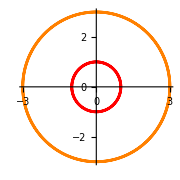
```mathematica
-Graphics-
Plot[f[t], {RangeVar, min,max}]
```

```mathematica
Plot3D[f[t,tt], f[t], {tt, min,max}]
```

```mathematica
(* 2D Primitives using the Wrapper Graphics *)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(* Plotting primitives *)
```

```mathematica
(* A single point  *)
```

```mathematica
Graphics[{PointSize[0.05],Red,Point[{1,2}]} , Axes->True, Background->White] 
(*option for the graphics place after the primitive function*)
```

```mathematica
Pn1 = Point[{1,2}, VertexColors->Red] (*get data strucutre visualization of Pn1 -> can pass to graphics function*)
```

```mathematica
Graphics[{Pn1, PointSize[0.1] (*wrong place for definition*)}, Axes->True (*definine graphics option here*)]
```

```mathematica
Graphics[{ PointSize[0.1](*definine the point size here IN FRONT*), Pn1 } (*put everything in curly bracket*), Axes->True (*definine graphics option here*)]
```

```mathematica
Graphics[{PointSize[0.15],Point[{1,2}]},PlotRange->3,Axes->True]
```

```mathematica
(* Point size, color, axes. Pn1 a point with coordinates {1,2} *)
```

```mathematica
Pn1=Point[{1,2},VertexColors->Red] (*defnine colour in primitive function*)
```

```mathematica
(* Plot Pn1 *)
```

```mathematica
Graphics[{PointSize[0.05],Pn1}, Axes->True]
```

```mathematica
Graphics[Pn1, Axes->True]
```

```mathematica
(* Multiple points, one color , pair of coordinate*)
```

```mathematica
Pn2={{1,2},{3,4},{2,-1}}
```

```mathematica
Graphics[{Red,PointSize[0.1],Point[Pn2]}, Axes->True,AspectRatio->1, Background->White] (*defnine colour in graphics option -> all point becomes red*)
```

```mathematica
(* Different colors for different points *)
```

```mathematica
Col={Red,Green,Orange}
```

```mathematica
Graphics[{PointSize[0.1],Point[Pn2,VertexColors->Col (*at each of the point, we want to colour it based on the list of colour*)]},
 Axes->True,AspectRatio->1, Background->White]
```

```mathematica
plotPoint[colour_]:=Graphics[{PointSize[0.1],colour,Point[Pn2]},
 Axes->True,AspectRatio->1, Background->White]
```

```mathematica
plotPoint[Red]
```

```mathematica
(* Example 2 Combine Plots of functions and primitives Using a wrapper
 Plot the spiral Spi[t_] (L1). Indicate the starting point (t=0) by red and the ending point (t=2 Pi by blue *)
```

```mathematica
RC[t_]:=R(2Pi-t)/(2Pi) (*radius change based on t*)
```

```mathematica
xt2[t_]:=RC[t]  Cos[t]
```

```mathematica
yt2[t_]:=RC[t] Sin[t]
```

```mathematica
Spi[t_]:={xt2[t],yt2[t]}
```

```mathematica
ParametricPlot[Spi[t],{t,0,2 Pi},Background->White]
```

```mathematica
(*Points PS (start) PE (end) displayed as primitives *)
```

```mathematica
PS=Spi[0] (*point start -> primitive functin Spiral*)
```

```mathematica
PE=Spi[2 Pi] (*point end*)
```

```mathematica
(* Both points *)
```

```mathematica
PP={PS,PE} (*pair of coordinate*)
```

```mathematica
(* Primitives without the wrapper Graphics *)
```

```mathematica
PSEG={PointSize[0.1],Point[PP,VertexColors->{Red, Green} (*start red, end green*)]}
```

```mathematica
(* Wrapper *)
```

```mathematica
PSE=Graphics[PSEG,Axes->True,AspectRatio->1]
```

```mathematica
PSp1=ParametricPlot[Spi[t],{t,0,2 Pi}, Axes->True,AspectRatio->1]
```

```mathematica
Show[{PSE,PSp1}]
```

```mathematica
(* Convert graphic objects into a collection of primitives (no wrapper) Important  *)
```

```mathematica
(* We will discuss here the structure of graphics objects represented by a list of primitives and options )
```

```mathematica
PSp1=ParametricPlot[Spi[t],{t,0,2 Pi}, Axes->True,AspectRatio->1]
```

```mathematica
PSp1[[1]];
```

```mathematica
PSp1[[2]] (*meta data of the parametric plot*)
```

```mathematica
PSp1G=PSp1[[1]];(*line data structure information of the parametric plot*)
```

```mathematica
(* Wrapper for both primitives  *)
```

```mathematica
Graphics[{PSp1G,PSEG},Axes->True,AspectRatio->1]
```

```mathematica
(*if didn't extarct the spiral graph*)
```

```mathematica
PSp1=ParametricPlot[Spi[t],{t,0,2 Pi}, Axes->True,AspectRatio->1]
```

```mathematica
PSEG={PointSize[0.1],Point[PP,VertexColors->{Red, Green} (*start red, end green*)]}
```

```mathematica
Graphics[{PSp1,PSEG},Axes->True,AspectRatio->1] (*error*)
```

```mathematica
Graphics[{PSp1[[1]],PSEG},Axes->True,AspectRatio->1, Background->White]
```

```mathematica
(* Function "Array"*)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(* Example 0 *)
```

```mathematica
Clear[f]
```

```mathematica
Array[f,5,{1,5}]
```

```mathematica
Array[f, 10, {0,1.}]
```

```mathematica
(* Create an array of 10 points {x,y} where x runs from 0 to 1 and y=Sin[x^2] *)
```

```mathematica
f[x_]:={x,Sin[x^2]} (*show pair of input and output*)
```

```mathematica
P10=Array[f, 10, {0,1.}]
```

```mathematica
(* RandomColor[] -returns a random RGB color *)
```

```mathematica
(* fPoint generates a single point or a collection of points P with the Random Colors *)
```

```mathematica
fPoint[P_]:=Point[P,VertexColors->RandomColor[]]
```

```mathematica
fPoint[{0,2}] 
(* only accept 1 point - good for run time assignment*)
```

```mathematica
fPoint[{0,2}, {2,3}] (*error in colour assignment*)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(* Example 0 *)
```

```mathematica
Map[f,{1,3,4,5}]
```

```mathematica
Map[Sin,{0,Pi/4,3Pi/2}]
```

```mathematica
(* Example 1 Two Random points with Random Colors  *)
```

```mathematica
fPoint[P_]:=Point[P,VertexColors->RandomColor[]]
```

```mathematica
xxx =fPoint[{{1,2},{5,6}}] (*this will plot as black*)
```

```mathematica
Graphics[{PointSize[0.1],xxx},
Axes->True, Background->White]
```

```mathematica
P2=Map[fPoint,{{1,2},{5,6}}]
```

```mathematica
Graphics[{PointSize[0.1],P2},
Background->White,Axes->True]
```

```mathematica
(* Apply fPoint to P10 *)
```

```mathematica
f[x_]:={x,Sin[x^2]} (*show pair of input and output*)
```

```mathematica
P10=Array[f, 10, {0,1.}]
```

```mathematica
GP10=Map[fPoint,P10]
```

```mathematica
(* Plot points *)
```

```mathematica
GPoints=Graphics[{PointSize[0.1],GP10}]
```

```mathematica
(*generate 10 points along the line y = x^2 from range 0 to 5, using different colour for the point
and plot it with a line to show overlapping*)
```

```mathematica
(*plot line*)
```

```mathematica
line[x_]:= x^2
```

```mathematica
linePlot = Plot[line[x], {x,0,5}, Background->White]
```

```mathematica
(*generate 10 coordinate*)
```

```mathematica
pointLine[x_] := {x, line[x]}
```

```mathematica
pointArray = Array[pointLine,10,{0,5}]
```

```mathematica
point[p_] := Point[p, VertexColors->RandomColor[]]
```

```mathematica
(*map the 10 coordinate to get point data structure*)
```

```mathematica
pointMapped = Map[point,pointArray]
```

```mathematica
(*primitive option for displaying point*)
```

```mathematica
pointInfo = {PointSize[0.05], pointMapped}
```

```mathematica
Graphics[{ linePlot[[1]], pointInfo},Axes->True, Background->White, AspectRatio->1]
```

```mathematica
pointPlot = Graphics[{ pointInfo},Axes->True, Background->White, AspectRatio->1]
```

```mathematica
Show[{linePlot, pointPlot}, Background->White, AspectRatio->1]
```

```mathematica
""
```

```mathematica
(* Example 4 Recall that points and vectors represent the same mathematical entities. 
Let us depict points P10 as vectors using the function "Arrow"  *)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(* Example 4.1 The basic arrow  *)
```

```mathematica
A0=Arrow[{{1,0},{4,1}}]
```

```mathematica
Graphics[{Red,A0}, Axes->True]
```

```mathematica
(* Example 4.1 Sequence of arrows  *)
```

```mathematica
A1=Arrow[{{1,0},{2,1},{3,0},{4,1}}];
```

```mathematica
Graphics[{Blue,A1}, Axes->True]
```

```mathematica
(* Example 4.2 As apposed to 2 arrows (the same data is used)   *)
```

```mathematica
A2={Arrow[{{1,0},{2,1}}],Arrow[{{3,0},{4,1}}]}; (*list contains 2 arrows)*)
```

```mathematica
Graphics[A2, Axes->True]
```

```mathematica
(* A convert a point  into the vector *)
```

```mathematica
Clear[fCArrow]
```

```mathematica
(* Create an arrow from 0 to P} *)
```

```mathematica
fCArrow[P_]:=Arrow[{{0,0},P}]
```

```mathematica
A3=Map[fCArrow,{{1,2},{5,6}}] (*2 arrows with same origin*)
```

```mathematica
Graphics[{A3},Axes->True,AspectRatio->1, Background->White]
```

```mathematica
(* Apply to P10 *)
```

```mathematica
P10=Array[f, 10, {0,1.}]
```

```mathematica
Vectors1=Map[fCArrow,P10]
```

```mathematica
(* Plot Vectors *)
```

```mathematica
GArrows=Graphics[{Arrowheads[Medium],Vectors1},Axes->True,AspectRatio->1,ImageSize->Small, Background->White]
```

```mathematica
Show[GPoints,GArrows] (*combine more than 1 graph together*)
```

```mathematica
(* Example 5 Connects the points into a sequence of arrows/lines  *)
```

```mathematica
GLines=Graphics[Line[P10],ImageSize->Small,Axes->True]
```

```mathematica
(* Output *)
```

```mathematica
Show[{GLines,GPoints}]
```

```mathematica
(*  Self-study  Example 6 Sample the function f= {Sin[3 x], Sin[2 x]}  with the step Pi/10. Plot triangle around every sample point *)
```

```mathematica
Clear[fS]
```

```mathematica
fS[x_]:={Sin[3 x ], Sin[2 x]}
```

```mathematica
G0=ParametricPlot[fS[t],{t,0,2Pi}]
```

```mathematica
(* Change the variable for sampling from 0, to 19 (20 points)*)
```

```mathematica
n=40;
```

```mathematica
Clear[fs1]
```

```mathematica
fs1[x_]:=fS[2Pi(x-1)/(n-1)]
```

```mathematica
(* Sample *)
```

```mathematica
Sf=1.0Array[fs1,n] (*create n points*)
```

```mathematica
G1=Graphics[{Red,PointSize[0.02],Point[Sf]},Axes->True] (*plot points*)
```

```mathematica
Show[G1,G0] (*combine 2 graph together*)
```

```mathematica
(* In order to plot an equilateral triangle we use the functions CirclePoints and Polygon  *)
```

```mathematica
(*-Graphics-*)
```

```mathematica
Tri=CirclePoints[0.1,3]
```

```mathematica
(* Check using Polygon  *)
```

```mathematica
GTri=Graphics[{Blue,Polygon[Tri]},Axes->True,PlotRange->1]
```

```mathematica
Something = CirclePoints[3]
```

```mathematica
Graphics[{Pink,Polygon[Something]},Axes->True,PlotRange->1]
```

```mathematica
Tri2=CirclePoints[1,10];
```

```mathematica
GTri2=Graphics[{Red,Polygon[Tri2]},Axes->True,PlotRange->1]
```

```mathematica
(* Calculate coordinates of each triangle  *)
```

```mathematica
Tri=CirclePoints[1.,5]
```

```mathematica
CT[i_]:={Tri[[1]]+Sf[[i]],Tri[[2]]+Sf[[i]],Tri[[3]]+Sf[[i]]}
```

```mathematica
CT[1]
```

```mathematica
Graphics[Polygon[CT[3]],Axes->True,PlotRange->1]
```

```mathematica
P40=Polygon[Array[CT,n]]
```

```mathematica
P40
```

```mathematica
G2=Graphics[{Purple,P40}] (*plot points*)
```

```mathematica
(* Check and compare *)
```

```mathematica
Show[G0,G2,G1]
```

```mathematica
(* Change the triangle to circle *)
```

```mathematica
CC[i_]:=Sf[[i]]
```

```mathematica
fC[i_]:=Circle[CC[i],0.1]
```

```mathematica
CCC=Array[fC,n]; (* array of circle primitive *)
```

```mathematica
G4=Graphics[{Purple,CCC}]
```

```mathematica
Show[G0,G1,G4]
```